# CurrencyConvert

“CurrencyConvert calls InflationAdjust under the hood for such conversions.InflationAdjust in turn calls Alpha API to get the data from CalculateFinancialData, but the API only returns a single value, not a time series.”

```mathematica
data=Table[{date,QuantityMagnitude@CurrencyConvert[Quantity[1,DatedUnit["USDollars",date]],DatedUnit["SwissFrancs",date]]},{date,DateRange[Today-Quantity[1,"Years"],Today]}]
```

InflationAdjust::insfferd: Cannot fetch exchange rate conversion data for USDollars to SwissFrancs for {2016,3,5}.

InflationAdjust::insfferd: Cannot fetch exchange rate conversion data for USDollars to SwissFrancs for {2016,3,6}.

InflationAdjust::insfferd: Cannot fetch exchange rate conversion data for USDollars to SwissFrancs for {2016,3,12}.

General::stop: Further output of InflationAdjust::insfferd will be suppressed during this calculation.

{{Fri 4 Mar 2016,0.99343},{Sat 5 Mar 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 6 Mar 2016,QuantityMagnitude[Missing[NotAvailable]]},{Mon 7 Mar 2016,0.99535},{Tue 8 Mar 2016,0.995795},{Wed 9 Mar 2016,0.997305},{Thu 10 Mar 2016,0.98505},{Fri 11 Mar 2016,0.98275},{Sat 12 Mar 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 13 Mar 2016,0.983049},{Mon 14 Mar 2016,0.9874},{Tue 15 Mar 2016,0.98701},{Wed 16 Mar 2016,0.97815},{Thu 17 Mar 2016,0.96735},{Fri 18 Mar 2016,0.96963},{Sat 19 Mar 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 20 Mar 2016,0.96985},{Mon 21 Mar 2016,0.97061},{Tue 22 Mar 2016,0.973},{Wed 23 Mar 2016,0.97555},{Thu 24 Mar 2016,0.975775},{Fri 25 Mar 2016,0.97725},{Sat 26 Mar 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 27 Mar 2016,0.977649},{Mon 28 Mar 2016,0.97385},{Tue 29 Mar 2016,0.9666},{Wed 30 Mar 2016,0.96495},{Thu 31 Mar 2016,0.9619},{Fri 1 Apr 2016,0.95875},{Sat 2 Apr 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 3 Apr 2016,0.958049},{Mon 4 Apr 2016,0.95885},{Tue 5 Apr 2016,0.95613},{Wed 6 Apr 2016,0.9563},{Thu 7 Apr 2016,0.95564},{Fri 8 Apr 2016,0.95373},{Sat 9 Apr 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 10 Apr 2016,0.95265},{Mon 11 Apr 2016,0.95497},{Tue 12 Apr 2016,0.9554},{Wed 13 Apr 2016,0.96678},{Thu 14 Apr 2016,0.96715},{Fri 15 Apr 2016,0.968035},{Sat 16 Apr 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 17 Apr 2016,0.96675},{Mon 18 Apr 2016,0.9646},{Tue 19 Apr 2016,0.962005},{Wed 20 Apr 2016,0.971885},{Thu 21 Apr 2016,0.97495},{Fri 22 Apr 2016,0.97885},{Sat 23 Apr 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 24 Apr 2016,0.97925},{Mon 25 Apr 2016,0.9752},{Tue 26 Apr 2016,0.97375},{Wed 27 Apr 2016,0.97118},{Thu 28 Apr 2016,0.966525},{Fri 29 Apr 2016,0.9592},{Sat 30 Apr 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 1 May 2016,0.958249},{Mon 2 May 2016,0.954895},{Tue 3 May 2016,0.95492},{Wed 4 May 2016,0.95765},{Thu 5 May 2016,0.9684},{Fri 6 May 2016,0.97175},{Sat 7 May 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 8 May 2016,0.972749},{Mon 9 May 2016,0.971365},{Tue 10 May 2016,0.975955},{Wed 11 May 2016,0.97105},{Thu 12 May 2016,0.971025},{Fri 13 May 2016,0.9749},{Sat 14 May 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 15 May 2016,0.975049},{Mon 16 May 2016,0.97769},{Tue 17 May 2016,0.98055},{Wed 18 May 2016,0.98775},{Thu 19 May 2016,0.99076},{Fri 20 May 2016,0.99103},{Sat 21 May 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 22 May 2016,0.990649},{Mon 23 May 2016,0.9893},{Tue 24 May 2016,0.9934},{Wed 25 May 2016,0.9913},{Thu 26 May 2016,0.98926},{Fri 27 May 2016,0.99453},{Sat 28 May 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 29 May 2016,0.99455},{Mon 30 May 2016,0.99225},{Tue 31 May 2016,0.99379},{Wed 1 Jun 2016,0.9886},{Thu 2 Jun 2016,0.99045},{Fri 3 Jun 2016,0.976225},{Sat 4 Jun 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 5 Jun 2016,0.97595},{Mon 6 Jun 2016,0.97065},{Tue 7 Jun 2016,0.9654},{Wed 8 Jun 2016,0.95909},{Thu 9 Jun 2016,0.96465},{Fri 10 Jun 2016,0.96435},{Sat 11 Jun 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 12 Jun 2016,0.96495},{Mon 13 Jun 2016,0.96435},{Tue 14 Jun 2016,0.9637},{Wed 15 Jun 2016,0.96165},{Thu 16 Jun 2016,0.96515},{Fri 17 Jun 2016,0.95985},{Sat 18 Jun 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 19 Jun 2016,0.96325},{Mon 20 Jun 2016,0.96232},{Tue 21 Jun 2016,0.96265},{Wed 22 Jun 2016,0.958535},{Thu 23 Jun 2016,0.96301},{Fri 24 Jun 2016,0.973925},{Sat 25 Jun 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 26 Jun 2016,0.9734},{Mon 27 Jun 2016,0.97773},{Tue 28 Jun 2016,0.980286},{Wed 29 Jun 2016,0.9798},{Thu 30 Jun 2016,0.97605},{Fri 1 Jul 2016,0.9733},{Sat 2 Jul 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 3 Jul 2016,0.974349},{Mon 4 Jul 2016,0.971115},{Tue 5 Jul 2016,0.9774},{Wed 6 Jul 2016,0.975335},{Thu 7 Jul 2016,0.97925},{Fri 8 Jul 2016,0.98385},{Sat 9 Jul 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 10 Jul 2016,0.98315},{Mon 11 Jul 2016,0.98298},{Tue 12 Jul 2016,0.988915},{Wed 13 Jul 2016,0.9852},{Thu 14 Jul 2016,0.98107},{Fri 15 Jul 2016,0.982935},{Sat 16 Jul 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 17 Jul 2016,0.98215},{Mon 18 Jul 2016,0.982335},{Tue 19 Jul 2016,0.985615},{Wed 20 Jul 2016,0.987425},{Thu 21 Jul 2016,0.985675},{Fri 22 Jul 2016,0.98751},{Sat 23 Jul 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 24 Jul 2016,0.98745},{Mon 25 Jul 2016,0.98579},{Tue 26 Jul 2016,0.992065},{Wed 27 Jul 2016,0.987375},{Thu 28 Jul 2016,0.980725},{Fri 29 Jul 2016,0.96929},{Sat 30 Jul 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 31 Jul 2016,0.96925},{Mon 1 Aug 2016,0.96803},{Tue 2 Aug 2016,0.964735},{Wed 3 Aug 2016,0.97315},{Thu 4 Aug 2016,0.97435},{Fri 5 Aug 2016,0.980075},{Sat 6 Aug 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 7 Aug 2016,0.98065},{Mon 8 Aug 2016,0.982985},{Tue 9 Aug 2016,0.981385},{Wed 10 Aug 2016,0.974625},{Thu 11 Aug 2016,0.9758},{Fri 12 Aug 2016,0.97504},{Sat 13 Aug 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 14 Aug 2016,0.974749},{Mon 15 Aug 2016,0.97303},{Tue 16 Aug 2016,0.96198},{Wed 17 Aug 2016,0.962375},{Thu 18 Aug 2016,0.95475},{Fri 19 Aug 2016,0.959295},{Sat 20 Aug 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 21 Aug 2016,0.96015},{Mon 22 Aug 2016,0.96183},{Tue 23 Aug 2016,0.96314},{Wed 24 Aug 2016,0.966815},{Thu 25 Aug 2016,0.96795},{Fri 26 Aug 2016,0.97828},{Sat 27 Aug 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 28 Aug 2016,0.978549},{Mon 29 Aug 2016,0.978535},{Tue 30 Aug 2016,0.98362},{Wed 31 Aug 2016,0.983555},{Thu 1 Sep 2016,0.97995},{Fri 2 Sep 2016,0.980335},{Sat 3 Sep 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 4 Sep 2016,0.98035},{Mon 5 Sep 2016,0.97995},{Tue 6 Sep 2016,0.96975},{Wed 7 Sep 2016,0.96985},{Thu 8 Sep 2016,0.97235},{Fri 9 Sep 2016,0.975425},{Sat 10 Sep 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 11 Sep 2016,0.97545},{Mon 12 Sep 2016,0.97195},{Tue 13 Sep 2016,0.97735},{Wed 14 Sep 2016,0.97299},{Thu 15 Sep 2016,0.97203},{Fri 16 Sep 2016,0.98075},{Sat 17 Sep 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 18 Sep 2016,0.980249},{Mon 19 Sep 2016,0.98015},{Tue 20 Sep 2016,0.97915},{Wed 21 Sep 2016,0.97415},{Thu 22 Sep 2016,0.96862},{Fri 23 Sep 2016,0.96995},{Sat 24 Sep 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 25 Sep 2016,0.969649},{Mon 26 Sep 2016,0.969195},{Tue 27 Sep 2016,0.970755},{Wed 28 Sep 2016,0.97138},{Thu 29 Sep 2016,0.96605},{Fri 30 Sep 2016,0.97137},{Sat 1 Oct 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 2 Oct 2016,0.96985},{Mon 3 Oct 2016,0.973745},{Tue 4 Oct 2016,0.979},{Wed 5 Oct 2016,0.97415},{Thu 6 Oct 2016,0.980855},{Fri 7 Oct 2016,0.977475},{Sat 8 Oct 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 9 Oct 2016,0.97885},{Mon 10 Oct 2016,0.983135},{Tue 11 Oct 2016,0.988775},{Wed 12 Oct 2016,0.99056},{Thu 13 Oct 2016,0.986375},{Fri 14 Oct 2016,0.99046},{Sat 15 Oct 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 16 Oct 2016,0.99015},{Mon 17 Oct 2016,0.988715},{Tue 18 Oct 2016,0.989955},{Wed 19 Oct 2016,0.98894},{Thu 20 Oct 2016,0.992825},{Fri 21 Oct 2016,0.99345},{Sat 22 Oct 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 23 Oct 2016,0.99465},{Mon 24 Oct 2016,0.9948},{Tue 25 Oct 2016,0.995},{Wed 26 Oct 2016,0.99364},{Thu 27 Oct 2016,0.993499},{Fri 28 Oct 2016,0.98758},{Sat 29 Oct 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 30 Oct 2016,0.98735},{Mon 31 Oct 2016,0.9891},{Tue 1 Nov 2016,0.97445},{Wed 2 Nov 2016,0.97355},{Thu 3 Nov 2016,0.974095},{Fri 4 Nov 2016,0.96896},{Sat 5 Nov 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 6 Nov 2016,QuantityMagnitude[Missing[NotAvailable]]},{Mon 7 Nov 2016,0.974285},{Tue 8 Nov 2016,0.97791},{Wed 9 Nov 2016,0.98445},{Thu 10 Nov 2016,0.98785},{Fri 11 Nov 2016,0.98811},{Sat 12 Nov 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 13 Nov 2016,QuantityMagnitude[Missing[NotAvailable]]},{Mon 14 Nov 2016,0.99802},{Tue 15 Nov 2016,1.00177},{Wed 16 Nov 2016,1.00202},{Thu 17 Nov 2016,1.00716},{Fri 18 Nov 2016,1.01014},{Sat 19 Nov 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 20 Nov 2016,QuantityMagnitude[Missing[NotAvailable]]},{Mon 21 Nov 2016,1.00876},{Tue 22 Nov 2016,1.01127},{Wed 23 Nov 2016,1.01681},{Thu 24 Nov 2016,1.01655},{Fri 25 Nov 2016,1.0143},{Sat 26 Nov 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 27 Nov 2016,QuantityMagnitude[Missing[NotAvailable]]},{Mon 28 Nov 2016,1.01315},{Tue 29 Nov 2016,1.01172},{Wed 30 Nov 2016,1.0175},{Thu 1 Dec 2016,1.01055},{Fri 2 Dec 2016,1.01075},{Sat 3 Dec 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 4 Dec 2016,QuantityMagnitude[Missing[NotAvailable]]},{Mon 5 Dec 2016,1.00652},{Tue 6 Dec 2016,1.01035},{Wed 7 Dec 2016,1.00735},{Thu 8 Dec 2016,1.0165},{Fri 9 Dec 2016,1.01745},{Sat 10 Dec 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 11 Dec 2016,QuantityMagnitude[Missing[NotAvailable]]},{Mon 12 Dec 2016,1.01334},{Tue 13 Dec 2016,1.01205},{Wed 14 Dec 2016,1.02029},{Thu 15 Dec 2016,1.0299},{Fri 16 Dec 2016,1.02712},{Sat 17 Dec 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 18 Dec 2016,QuantityMagnitude[Missing[NotAvailable]]},{Mon 19 Dec 2016,1.02728},{Tue 20 Dec 2016,1.02871},{Wed 21 Dec 2016,1.0269},{Thu 22 Dec 2016,1.02562},{Fri 23 Dec 2016,1.0278},{Sat 24 Dec 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 25 Dec 2016,QuantityMagnitude[Missing[NotAvailable]]},{Mon 26 Dec 2016,1.02715},{Tue 27 Dec 2016,1.0281},{Wed 28 Dec 2016,1.02845},{Thu 29 Dec 2016,1.0229},{Fri 30 Dec 2016,1.01835},{Sat 31 Dec 2016,QuantityMagnitude[Missing[NotAvailable]]},{Sun 1 Jan 2017,QuantityMagnitude[Missing[NotAvailable]]},{Mon 2 Jan 2017,1.02375},{Tue 3 Jan 2017,1.02744},{Wed 4 Jan 2017,1.02145},{Thu 5 Jan 2017,1.00965},{Fri 6 Jan 2017,1.0173},{Sat 7 Jan 2017,QuantityMagnitude[Missing[NotAvailable]]},{Sun 8 Jan 2017,QuantityMagnitude[Missing[NotAvailable]]},{Mon 9 Jan 2017,1.01519},{Tue 10 Jan 2017,1.01686},{Wed 11 Jan 2017,1.0141},{Thu 12 Jan 2017,1.01093},{Fri 13 Jan 2017,1.00915},{Sat 14 Jan 2017,QuantityMagnitude[Missing[NotAvailable]]},{Sun 15 Jan 2017,QuantityMagnitude[Missing[NotAvailable]]},{Mon 16 Jan 2017,1.01177},{Tue 17 Jan 2017,1.0016},{Wed 18 Jan 2017,1.00756},{Thu 19 Jan 2017,1.00623},{Fri 20 Jan 2017,1.0023},{Sat 21 Jan 2017,QuantityMagnitude[Missing[NotAvailable]]},{Sun 22 Jan 2017,QuantityMagnitude[Missing[NotAvailable]]},{Mon 23 Jan 2017,0.9963},{Tue 24 Jan 2017,1.00093},{Wed 25 Jan 2017,0.9994},{Thu 26 Jan 2017,0.9999},{Fri 27 Jan 2017,0.9992},{Sat 28 Jan 2017,QuantityMagnitude[Missing[NotAvailable]]},{Sun 29 Jan 2017,QuantityMagnitude[Missing[NotAvailable]]},{Mon 30 Jan 2017,0.99536},{Tue 31 Jan 2017,0.989155},{Wed 1 Feb 2017,0.993025},{Thu 2 Feb 2017,0.992755},{Fri 3 Feb 2017,0.99263},{Sat 4 Feb 2017,QuantityMagnitude[Missing[NotAvailable]]},{Sun 5 Feb 2017,QuantityMagnitude[Missing[NotAvailable]]},{Mon 6 Feb 2017,0.99088},{Tue 7 Feb 2017,0.997661},{Wed 8 Feb 2017,0.99464},{Thu 9 Feb 2017,1.00166},{Fri 10 Feb 2017,1.00295},{Sat 11 Feb 2017,QuantityMagnitude[Missing[NotAvailable]]},{Sun 12 Feb 2017,QuantityMagnitude[Missing[NotAvailable]]},{Mon 13 Feb 2017,1.00579},{Tue 14 Feb 2017,1.00608},{Wed 15 Feb 2017,1.00547},{Thu 16 Feb 2017,0.997085},{Fri 17 Feb 2017,1.00293},{Sat 18 Feb 2017,QuantityMagnitude[Missing[NotAvailable]]},{Sun 19 Feb 2017,QuantityMagnitude[Missing[NotAvailable]]},{Mon 20 Feb 2017,1.00276},{Tue 21 Feb 2017,1.00964},{Wed 22 Feb 2017,1.0103},{Thu 23 Feb 2017,1.00641},{Fri 24 Feb 2017,1.00748},{Sat 25 Feb 2017,QuantityMagnitude[Missing[NotAvailable]]},{Sun 26 Feb 2017,QuantityMagnitude[Missing[NotAvailable]]},{Mon 27 Feb 2017,1.00896},{Tue 28 Feb 2017,1.00587},{Wed 1 Mar 2017,1.00891},{Thu 2 Mar 2017,1.0134},{Fri 3 Mar 2017,1.00884},{Sat 4 Mar 2017,QuantityMagnitude[Missing[NotAvailable]]}}

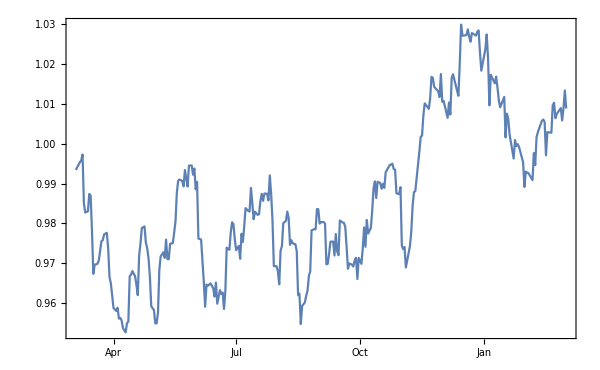

```mathematica
DateListPlot[Cases[data,{_,_?NumericQ}],ImageSize-> 600]
```

## References

```mathematica
?TimeSeries
```

RowBox[{"TimeSeries", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["t", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["t", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]]}], "}"}], StyleBox["…", "TR"]}]}], "}"}], "]"}] represents a time series specified by time-value pairs RowBox[{"{", RowBox[{SubscriptBox[StyleBox["t", "TI"], StyleBox["i", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]]}], "}"}].
RowBox[{"TimeSeries", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["tspec", "TI"]}], "]"}] represents a time series with values SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]] at times specified by StyleBox["tspec", "TI"].

```mathematica
?DateRange
```

RowBox[{"DateRange", "[", RowBox[{SubscriptBox[StyleBox["date", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["date", "TI"], StyleBox["2", "TR"]]}], "]"}] gives all dates in the range from StyleBox[SubscriptBox["date", StyleBox["1", "TR"]], "TI"] to StyleBox[SubscriptBox["date", StyleBox["2", "TR"]], "TI"].
RowBox[{"DateRange", "[", RowBox[{SubscriptBox[StyleBox["date", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["date", "TI"], StyleBox["2", "TR"]], ",", StyleBox["increment", "TI"]}], "]"}] gives the date lists in the range from StyleBox[SubscriptBox["date", StyleBox["1", "TR"]], "TI"] to StyleBox[SubscriptBox["date", StyleBox["2", "TR"]], "TI"] that are StyleBox["increment", "TI"] apart.

```mathematica
?Today
```

Today gives a DateObject representing the current day.